```mathematica
Set 15: Game Theory
```

## Matrix Games

The functions that give optimal row and column strategies for a matrix game are below:

```mathematica
RowStrategy[P_]:=Module[{d=Dimensions@P,L},(L=LinearProgramming[Table[1,d[[1]]],Transpose@P+1-Min@P,Table[1,d[[2]]]])/Total@L]
ColStrategy[P_]:=RowStrategy@Transpose[-P]
```

### Exercise Subsection

Morra is a rock-paper-scissors like hand game played between two players (see https://en.wikipedia.org/wiki/Morra_(game) ).  Here is one variant: each player shows 0,1,2,3,4, or 5 fingers on a hand and simultaneously guesses the total number of fingers shown between both players (a number between 0 and 10).  If exactly one player correctly guesses the total number of fingers, that player earns 1 from the loser.  

Therefore the strategies for each player are pairs {f,g} where f is the number of fingers shown and g is the number of fingers guessed.  Do the following to solve the game:
1. Create a list named strategies containing all pairs {f,g} where f is any number 0,...,5 and g is any number 0,...,10.
2. Define a function Payoff with input strategies s1 and s2 in strategies and output 1 if s1 wins, -1 if s2 wins, and 0 otherwise.
3. Create a payoff matrix s1, s2 entry given by Payoff[s1,s2] where s1 and s2 range over all strategies.
4. Apply RowStrategy (as defined in Lecture15) to solve the matrix game.

### Exercise Subsection

A two player game can be played on a graph G in this way:  Both players select vertices in G.  If the vertices are connected, then the first player earns 1 from the second player, otherwise the payoff is 0.  This is a matrix game with payoff matrix equal to AdjacencyMatrix@G.  Find optimal strategies for the row and column players when playing this game on each of the graphs in the list below:

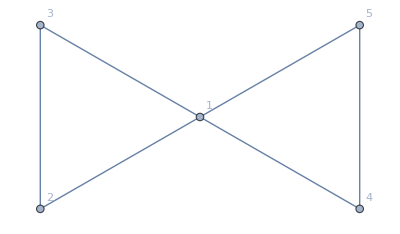
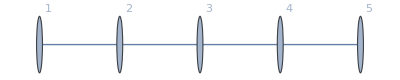
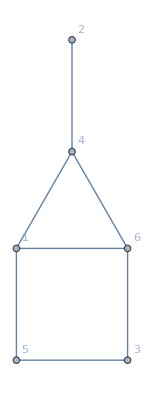
```mathematica
L={-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

## Nonzero sum games

### Exercise Subsection

Chicken is a two player game where each player tries to intimidate the other into yielding. Imaging two cars driving towards one another, with each driver hoping the other will swerve first.  The payoffs to player are given in the table below, with the entries giving the payoff to the row and column player, respectively.

```mathematica
chicken={{{0,0},{-1,2}},{{2,-1},{-100,-100}}};
TableForm[ToString/@#&/@chicken,TableHeadings->{{"Row 1: Swerve","Row 2: Drive"},{"Col 1: Swerve","Col 2: Drive"}}]
```

| Col 1: Swerve | Col 2: Drive
Row 1: Swerve | {0, 0} | {-1, 2}
Row 2: Drive | {2, -1} | {-100, -100}

We are having a chicken contest! 

Define a function Strategy[H_] with input H a sequence of 1’s and 2’s giving your opponent’s history of play and with output either 1 (swerve) or 2 (drive).  Change the name Strategy to another name (which will be seen by everyone else in class).  

Each submitted strategy will compete against every other submitted program a large, but undisclosed, number of rounds.  The tournament will be run in the same way as the prisoner’s dilemma example in Lecture 15, with the exception that the payoffs will change from the dilemma to chicken.

Good luck!

## Learning from experience

### Exercise Subsection

The integers in a random permutation of 1,2,...,100 are announced one at a time.  A player wins if they choose to “stop” after the integer 100 is announced.  However, the following strategy must be used:

1. An integer R is chosen before any numbers are announced. 
2. The first R integers announced are automatically rejected.
3. After that, “stop” is said if an integer is announced that is the largest integer announced so far.

The goal is to find the optimal value of R.  Approximate this value of R using the following steps:

1. Define a function GoodRValues[L_] that has input a permutation L of 1,...,100 and output the list integers R that will identify 100 using the above scheme.
2. Run GoodRValues many times on RandomSample@Range@100 to find the integer R that is most likely to identify 100.